```mathematica
x[t_]:=Cos[3t];
y[t_]:=Sin[t];

dydx[t_]:=D[y[t],t]/D[x[t],t];

d2ydx2[t_]:=D[dydx[t],t]/D[x[t],t];
```

```mathematica
dydx[t]
Solve[%==0 && 0 ≤ t ≤ 2Pi,t]
dydx[t]/.t->{0,Pi/2,Pi,3Pi/2}
d2ydx2[t]
Solve[%==0,t]
d2ydx2[t]/.t->{Pi/4,5Pi/4,2Pi}
```

-1/3 Cos[t] Csc[3 t]

{{t→π/2},{t→(3 π)/2}}

{ComplexInfinity,0,ComplexInfinity,0}

-1/3 Csc[3 t] (Cos[t] Cot[3 t] Csc[3 t]+1/3 Csc[3 t] Sin[t])

{{t→ConditionalExpression[-ArcTan[√((3-√3)/(1+√3))]+2 π C[1],C[1]∈Integers]},{t→ConditionalExpression[π-ArcTan[√((3-√3)/(1+√3))]+2 π C[1],C[1]∈Integers]},{t→ConditionalExpression[ArcTan[√((3-√3)/(1+√3))]+2 π C[1],C[1]∈Integers]},{t→ConditionalExpression[-π+ArcTan[√((3-√3)/(1+√3))]+2 π C[1],C[1]∈Integers]},{t→ConditionalExpression[ArcTan[-1/2 ⅈ √(-1+√3),-1/2 √(3+√3)]+2 π C[1],C[1]∈Integers]},{t→ConditionalExpression[ArcTan[-1/2 ⅈ √(-1+√3),(√(3+√3))/2]+2 π C[1],C[1]∈Integers]},{t→ConditionalExpression[ArcTan[1/2 ⅈ √(-1+√3),-1/2 √(3+√3)]+2 π C[1],C[1]∈Integers]},{t→ConditionalExpression[ArcTan[1/2 ⅈ √(-1+√3),(√(3+√3))/2]+2 π C[1],C[1]∈Integers]}}

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

{(2 √2)/9,-(2 √2)/9,Indeterminate}

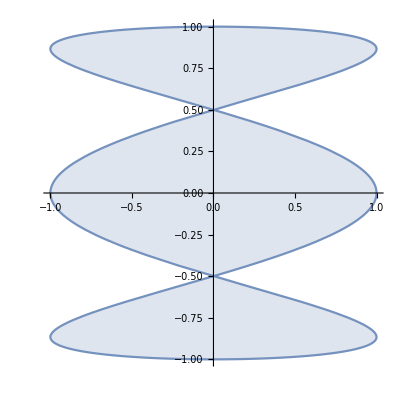

```mathematica
shadecolor=RGBColor[223/256,230/256,240/256,1];
linecolor = RGBColor[117/256,147/256,191/256,1];
shadecolor2=RGBColor[1,1,1,1];

ParametricPlot[{x[t],y[t]},{t,0,2Pi}]/.Line[l_List]:>{{shadecolor,Polygon[l]},{linecolor,Line[l]}}
```

```mathematica
NIntegrate[Sqrt[D[x[t],t]^2+D[y[t],t]^2],{t,0,2Pi}]
```

13.0654

```mathematica
Integrate[2(1-Cos[t])Sqrt[D[2(t-Sin[t]),t]^2+D[2(1-Cos[t]),t]^2],t]
```

8/3 (-9 Cos[t/2]+Cos[(3 t)/2]) Csc[t/2] √(Sin[t/2]^2)

```mathematica
Integrate[2(1-Cos[t])Sqrt[D[2(t-Sin[t]),t]^2+D[2(1-Cos[t])]],t]
```

1/(4 √2 √(-3+2 Cos[t]))√(4-5 Cos[t]+Cos[2 t]) Csc[t/2] (-30 Cos[t/2] √(-3+2 Cos[t])+4 √(-3+2 Cos[t]) Cos[(3 t)/2]+55 Log[2 Cos[t/2]+√(-3+2 Cos[t])])

```mathematica
?Polar
```

Information::notfound: Symbol Polar not found.

```mathematica
ToPolarCoordinates[{3,7}]
```

{√58,ArcTan[7/3]}

```mathematica
FromPolarCoordinates[{2,3}]
```

{2 Cos[3],2 Sin[3]}

```mathematica
FromPolarCoordinates[{r,θ}]
```

{r Cos[θ],r Sin[θ]}

```mathematica
PolarPlot[2Sin[2t],{t,0,2Pi},Filling->Axis]
```

PolarPlot::optx: Unknown option Filling→Axis in PolarPlot[2 Sin[2 t],{t,0,2 π},Filling→Axis].

PolarPlot[2 Sin[2 t],{t,0,2 π},Filling→Axis]

```mathematica
2Sin[2 Pi/3]
```

√3

```mathematica
1/2 Integrate[(2 Sin[2t])^2, {t,0,Pi/2}]
```

π/2

```mathematica
r[t_]:= 2Sin[2t]
drdt[t_]:=D[r[t],t]
r[t]
drdt[t]
Sqrt[r[t]^2+drdt[t]^2]
Integrate[Sqrt[r[t]^2+D[r[t],t]^2],{t,0,Pi}]
```

2 Sin[2 t]

4 Cos[2 t]

√(16 Cos[2 t]^2+4 Sin[2 t]^2)

8 EllipticE[3/4]

```mathematica
?PolarPlot
```

RowBox[{"PolarPlot", "[", RowBox[{StyleBox["r", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["θ", "TR"], ",", SubscriptBox[StyleBox["θ", "TR"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["θ", "TR"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a polar plot of a curve with radius StyleBox["r", "TI"] as a function of angle StyleBox["θ", "TR"].
RowBox[{"PolarPlot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["θ", "TR"], ",", SubscriptBox[StyleBox["θ", "TR"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["θ", "TR"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] makes a polar plot of curves with radius functions SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ….

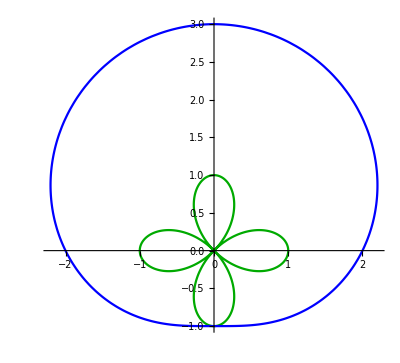

```mathematica
eqns[t_]:={Cos[2t],2+Sin[t]};
region=PolarPlot[Evaluate@eqns[t],{t,-π,π},RegionFunction->Function[{x,y,t,r},{#1>#2}&@@Re[eqns[t]]//First]];
pts=Cases[region,Line[x___]:>x,Infinity];
colors={Darker@Green,Blue};

Show[PolarPlot[Evaluate@eqns[t],{t,-π,π},PlotStyle->colors],ListLinePlot[pts,PlotStyle->colors,Filling->Axis,FillingStyle->LightGreen],PlotRange->All]
```

General::obspkg: VectorAnalysis` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

{√(x^2+y^2),ArcTan[x,y],z}

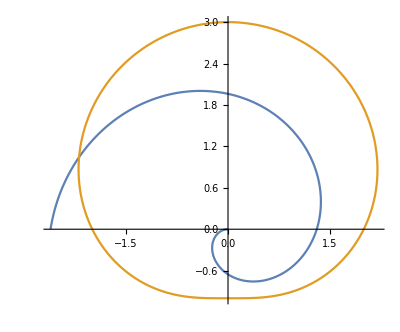

```mathematica
<<VectorAnalysis`;
{rho,t,z}=CoordinatesFromCartesian[{x,y,z},Cylindrical]
Quiet@Show[PolarPlot[{Cos@2t,2+Sin@t},{t,0,2Pi}],RegionPlot[Cos@2t>rho>2+Sin@t,{x,0,2},{y,-1,1}],Method->{"TransparentPolygonMesh"->True}]
```

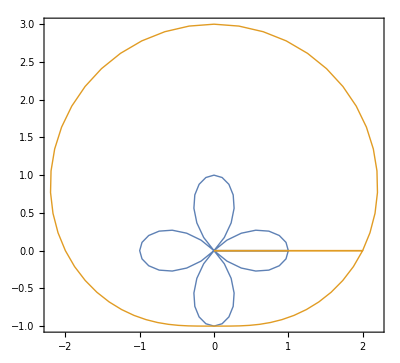

```mathematica
ρ[t_]:=Cos[2t];
σ[t_]:=2+Sin[t];
ParametricPlot[{{r Cos[t] ρ[t],r Sin[t] ρ[t]},{r Cos[t] σ[t],r Sin[t] σ[t]}},{t,0,2π},{r,0,1},PlotStyle->{{Opacity[.5],Red},{Opacity[1],White}},Mesh->None,PlotRange->All]
```

```mathematica
Needs["Presentations`Master`"]

trfill=Draw[{Sqrt[6 Cos[2 t]],Sqrt[3]},{t,-π/6,π/6},Filling->{1->{2}},FillingStyle->LightBlue];
Draw2D[{PolarDraw[{Sqrt[3],Sqrt[6 Cos[2 t]],-Sqrt[6 Cos[2 t]]},{t,0,2 Pi}],trfill/.DrawingTransform[#2 Cos[#1]&,#2 Sin[#1]&],trfill/.DrawingTransform[-#2 Cos[#1]&,#2 Sin[#1]&]},AspectRatio->Automatic,Frame->True,ImageSize->300]
```

Get::noopen: Cannot open Presentations`Master`.

Needs::nocont: Context Presentations`Master` was not created when Needs was evaluated.

$Failed

ReplaceAll::reps: {DrawingTransform[#2 Cos[#1]&,#2 Sin[#1]&]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {DrawingTransform[-#2 Cos[#1]&,#2 Sin[#1]&]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Draw2D[{PolarDraw[{√3,√6 √Cos[2 ArcTan[x,y]],-√6 √Cos[2 ArcTan[x,y]]},{ArcTan[x,y],0,2 π}],Draw[{√6 √Cos[2 ArcTan[x,y]],√3},{ArcTan[x,y],-π/6,π/6},Filling→{1→{2}},FillingStyle→RGBColor[0.87, 0.94, 1]]/.DrawingTransform[#2 Cos[#1]&,#2 Sin[#1]&],Draw[{√6 √Cos[2 ArcTan[x,y]],√3},{ArcTan[x,y],-π/6,π/6},Filling→{1→{2}},FillingStyle→RGBColor[0.87, 0.94, 1]]/.DrawingTransform[-#2 Cos[#1]&,#2 Sin[#1]&]},AspectRatio→Automatic,Frame→True,ImageSize→300]

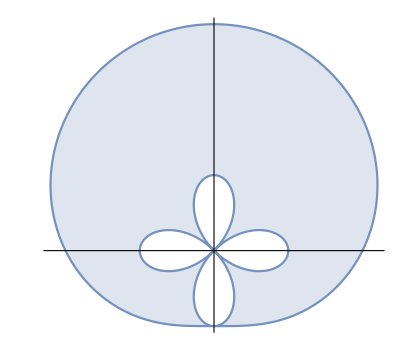

```mathematica
r[t_]:=2+Sin[t];
r2[t_]:=Cos[2t];
x[t_]:=r[t] Cos[t];
y[t_]:=r[t]Sin[t];
x2[t_]:=r2[t] Cos[t];
y2[t_]:=r2[t]Sin[t];

shadecolor=RGBColor[223/256,230/256,240/256,1]; (* light blue *)
linecolor = RGBColor[117/256,147/256,191/256,1]; (* dark blue *)
shadecolor2=RGBColor[1,1,1,1]; (* white *)

plot1=ParametricPlot[{x[t],y[t]},{t,0,2Pi+0.01},Ticks->None]/.Line[l_List]:>{{shadecolor,Polygon[l]},{linecolor,Line[l]}};
plot2=ParametricPlot[{x2[t],y2[t]},{t,0,2Pi+0.01},Ticks->None]/.Line[l_List]:>{{shadecolor2,Polygon[l]},{linecolor,Line[l]}};
Show[plot1,plot2]
```

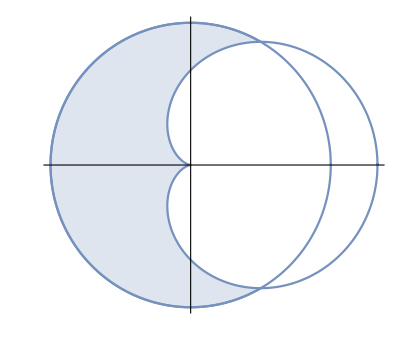

```mathematica
r[t_]:=3;
r2[t_]:=2(1+Cos[t]);
x[t_]:=r[t] Cos[t];
y[t_]:=r[t]Sin[t];
x2[t_]:=r2[t] Cos[t];
y2[t_]:=r2[t]Sin[t];

shadecolor=RGBColor[223/256,230/256,240/256,1];
linecolor = RGBColor[117/256,147/256,191/256,1];
shadecolor2=RGBColor[1,1,1,1];

plot1=ParametricPlot[{x[t],y[t]},{t,0,2Pi+0.01},Ticks->None,PlotRange->All]/.Line[l_List]:>{{shadecolor,Polygon[l]},{linecolor,Line[l]}};
plot2=ParametricPlot[{x2[t],y2[t]},{t,0,2Pi+0.01},Ticks->None,PlotRange->All]/.Line[l_List]:>{{shadecolor2,Polygon[l]},{linecolor,Line[l]}};
plot3=ParametricPlot[{x[t],y[t]},{t,0,2Pi+0.01},Ticks->None,PlotRange->All]/.Line[l_List]:>{{Transparent,Polygon[l]},{linecolor,Line[l]}};
(* plot3=Plot[{x,-x},{x,-3,3},PlotStyle->{Gray,Gray}]; *)
Show[plot1,plot2,plot3]
```

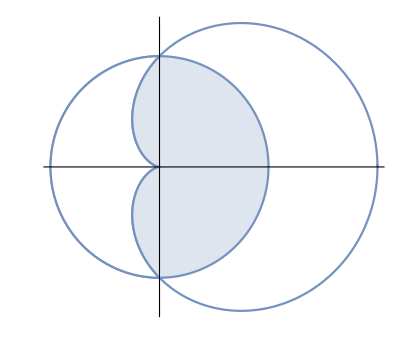

```mathematica
r[t_]:=1;
r2[t_]:=1+Cos[t];
x[t_]:=r[t] Cos[t];
y[t_]:=r[t]Sin[t];
x2[t_]:=r2[t] Cos[t];
y2[t_]:=r2[t]Sin[t];

shadecolor=RGBColor[223/256,230/256,240/256,1];
linecolor = RGBColor[117/256,147/256,191/256,1];
shadecolor2=RGBColor[1,1,1,1];

plot1=ParametricPlot[{x[t],y[t]},{t,0,2Pi+0.01},Ticks->None,PlotRange->All]/.Line[l_List]:>{{shadecolor,Polygon[l]},{linecolor,Line[l]}};
plot2=ParametricPlot[{x2[t],y2[t]},{t,0,2Pi+0.01},Ticks->None,PlotRange->All]/.Line[l_List]:>{{Transparent,Polygon[l]},{linecolor,Line[l]}};
plot3=ParametricPlot[{x[t],y[t]},{t,Pi/2,3Pi/2+0.01},Ticks->None,PlotRange->All]/.Line[l_List]:>{{shadecolor2,Polygon[l]},{linecolor,Line[l]}};
plot4=ParametricPlot[{x2[t],y2[t]},{t,Pi/2,3Pi/2+0.01},Ticks->None,PlotRange->All]/.Line[l_List]:>{{shadecolor,Polygon[l]},{linecolor,Line[l]}};
(* plot3=Plot[{x,-x},{x,-3,3},PlotStyle->{Gray,Gray}]; *)
Show[plot1,plot3,plot2,plot4]
```

```mathematica
ClearAll[t]
Solve[3==2(1+Cos[t])&&0≤t≤2Pi,t]
```

{{t→π/3},{t→(5 π)/3}}

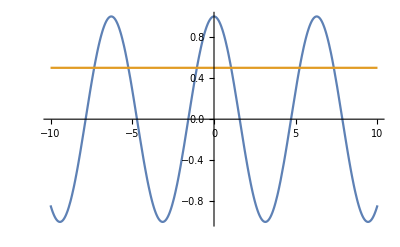

```mathematica
Plot[{Cos[x],1/2},{x,-10,10}]
```

```mathematica
r1=3;
r2=2(1+Cos[t]);

Integrate[r1^2-r2^2,{t,Pi/3,5Pi/3}]//N
```

28.1548

```mathematica
Integrate[r1^2,{t,0,2Pi}]//N
```

56.5487

```mathematica
DSolve[x Log[x] == (2 y[x] Sqrt[3+y[x]^2]) y'[x],y[x],x]
```

{{y[x]→-(√(-24-3 ⅈ 3^(1/6) ((-x^2+8 C[1]+2 x^2 Log[x])^2)^(1/3)-3^(2/3) ((-x^2+8 C[1]+2 x^2 Log[x])^2)^(1/3)))/(2 √2)},{y[x]→(√(-24-3 ⅈ 3^(1/6) ((-x^2+8 C[1]+2 x^2 Log[x])^2)^(1/3)-3^(2/3) ((-x^2+8 C[1]+2 x^2 Log[x])^2)^(1/3)))/(2 √2)},{y[x]→-(√(-24+3 ⅈ 3^(1/6) ((-x^2+8 C[1]+2 x^2 Log[x])^2)^(1/3)-3^(2/3) ((-x^2+8 C[1]+2 x^2 Log[x])^2)^(1/3)))/(2 √2)},{y[x]→(√(-24+3 ⅈ 3^(1/6) ((-x^2+8 C[1]+2 x^2 Log[x])^2)^(1/3)-3^(2/3) ((-x^2+8 C[1]+2 x^2 Log[x])^2)^(1/3)))/(2 √2)},{y[x]→-1/2 √(-12+3^(2/3) ((-x^2+8 C[1]+2 x^2 Log[x])^2)^(1/3))},{y[x]→1/2 √(-12+3^(2/3) ((-x^2+8 C[1]+2 x^2 Log[x])^2)^(1/3))}}

```mathematica
Integrate[x Log[x],x]
```

-x^2/4+1/2 x^2 Log[x]

```mathematica
Integrate[2 y Sqrt[3+y^2],y]
```

2/3 (3+y^2)^(3/2)

```mathematica
DSolve[y'''[x]+y''[x]+y'[x]+y[x]==0,y[x],x]
```

{{y[x]→ⅇ^-x C[3]+C[1] Cos[x]+C[2] Sin[x]}}

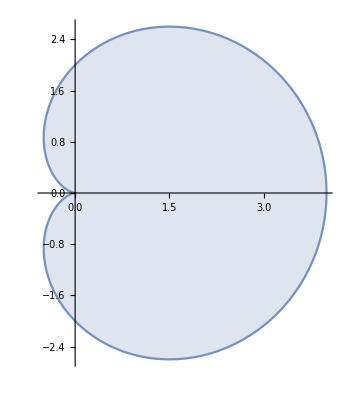

```mathematica
shadecolor=RGBColor[223/256,230/256,240/256,1];
linecolor = RGBColor[117/256,147/256,191/256,1];
shadecolor2=RGBColor[1,1,1,1];

PolarPlot[2(1+Cos[t]),{t,0,2Pi}]/.Line[l_List]:>{{shadecolor,Polygon[l]},{linecolor,Line[l]}}
```